Άσκηση 6.1

Υπολογίστε τη θέση (x_0,y_0) του σημείου L_4 στο σύστημα Ήλιος-Δίας (μ=0.001). Ολοκληρώστε τις εξισώσεις του RTBP για το μικρό σώμα αριθμητικά για t=200 t.u. και σχεδιάστε τις τροχιές στο περιστρεφόμενο σύστημα για τις παρακάτω αρχικές συνθήκες:

x(0)=x_0+0.0065, y(0)=y_0+0.0065, (ⅆx/ⅆt)(0)=0, (ⅆy/ⅆt)(0)=0 (tadpole orbit)

x(0)=-0.97668, y(0)=0, (ⅆx/ⅆt)(0)=0, (ⅆy/ⅆt)(0)=-0.06118 (horseshoe orbit)

Σε τι τιμή ενέργειας C_J αντιστοιχούν οι παραπάνω τροχιές;
Για τις παραπάνω τροχιές αυξήστε την τιμή της αρχικής συνθήκης (ⅆx/ⅆt). Για ποια τιμή της δεν παρατηρουμε πλέον τροχιές της μορφής tadopole ή horseshoe (σχεδιάστε αυτές τις τροχιές για κατάλληλο χρόνο ολοκλήρωσης);

Λύση

Υπολογίζουμε τη θέση του σημείο L_4(1/2-μ,(√3)/2).

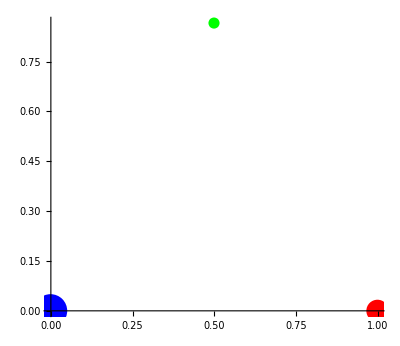

```mathematica
ClearAll["Global`*"]
μ=0.001;tmax=200;
x4=1/2-μ;y4=N@((√3)/2);
bodies=Graphics[{
Blue,PointSize[0.06],Point[{-μ,0}],
Red,PointSize[0.04],Point[{1-μ,0}],
Green,PointSize[0.02],Point[{x4,y4}](*,
Black,Text[Style["L_4("~~ToString@x4~~", "~~ToString@y4~~")",{14}],{1.05x4,1.05y4}]*)
},Axes->True,AxesOrigin->{0,0}]
```

Για το RTBP θεωρούμε ότι m_3→0. Οι εξισώσεις που περιγράφουν την κίνηση του m_3 στο περιστρεφόμενο σύστημα (τα m_1, m_2 παραμένουν σταθερά γιατί θεωρούμε κυκλική τροχιά για τα δύο σώματα αυτά) είναι:

x^(..)=2 ẏ+x-(1-μ)(x+μ)/r_1^3-μ(x-(1-μ))/r_2^3
y^(..)=-2 ẋ+y-(1-μ)y/r_1^3-μ y/r_2^3

όπου r_1=√((x+μ)^2+y^2), r_2=√((x-1+μ)^2+y^2)

```mathematica
r1[t]=√((x[t]+μ)^2+y[t]^2);r2[t]=√((x[t]-1+μ)^2+y[t]^2);
deq1=x''[t]==2y'[t]+x[t]-(1-μ)(x[t]+μ)/r1[t]^3-μ(x[t]-(1-μ))/r2[t]^3;
deq2=y''[t]==-2x'[t]+y[t]-(1-μ)y[t]/r1[t]^3-μ y[t]/r2[t]^3;
```

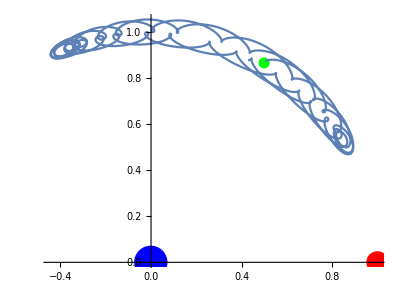

```mathematica
IVP1={deq1,deq2,x[0]==x4+0.0065,y[0]==y4+0.0065,x'[0]==0,y'[0]==0};
sol1=NDSolve[IVP1,{x[t],y[t]},{t,0,tmax}];
xx1=x[t]/.sol1[[1]];
yy1=y[t]/.sol1[[1]];
p1=ParametricPlot[{xx1,yy1},{t,0,tmax}];
Show[{bodies,p1}]
```

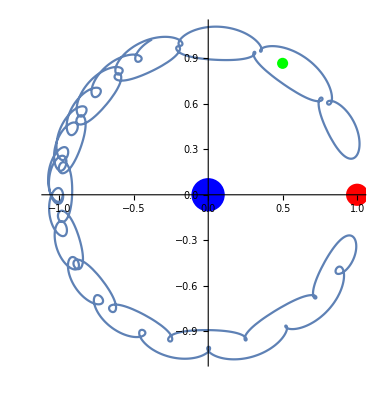

```mathematica
IVP2={deq1,deq2,x[0]==-0.97668,y[0]==0,x'[0]==0,y'[0]==-0.06118};
sol2=NDSolve[IVP2,{x[t],y[t]},{t,0,tmax}];
xx2=x[t]/.sol2[[1]];
yy2=y[t]/.sol2[[1]];
p2=ParametricPlot[{xx2,yy2},{t,0,tmax}];
Show[{bodies,p2}]
```

Η ενέργεια (ολοκλήρωμα Jacobi) υπολογίζεται για την κάθε τροχιά από την C_J=1/2((ẋ)^2+(ẏ)^2)-((1-μ)/r_1+μ/r_2)-1/2(x^2+y^2).

```mathematica
Cj[x_,y_,ux_,uy_]:=1/2(ux^2+uy^2)-((1-μ)/(√((x+μ)^2+y^2))+μ/(√((x-1+μ)^2+y^2)))-1/2(x^2+y^2)
StringForm["1^η τροχιά: C_J=``",Cj[x4+0.0065,y4+0.0065,0,0]]
StringForm["2^η τροχιά: C_J=``",Cj[-0.97668,0,0,-0.6118]]
```

1^η τροχιά: C_J=-1.49962

2^η τροχιά: C_J=-1.31421

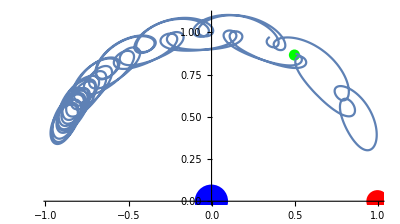

```mathematica
IVP3={deq1,deq2,x[0]==x4+0.0065,y[0]==y4+0.0065,x'[0]==0.050,y'[0]==0};
sol3=NDSolve[IVP3,{x[t],y[t]},{t,0,tmax}];
xx3=x[t]/.sol3[[1]];
yy3=y[t]/.sol3[[1]];
p3=ParametricPlot[{xx3,yy3},{t,0,tmax}];
Show[{bodies,p3}]
```

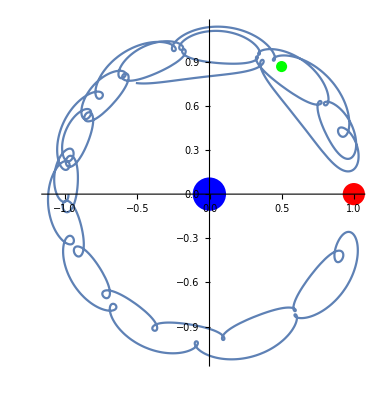

```mathematica
IVP4={deq1,deq2,x[0]==-0.97668,y[0]==0,x'[0]==0.005,y'[0]==-0.06118};
sol4=NDSolve[IVP4,{x[t],y[t]},{t,0,tmax}];
xx4=x[t]/.sol4[[1]];
yy4=y[t]/.sol4[[1]];
p4=ParametricPlot[{xx4,yy4},{t,0,tmax}];
Show[{bodies,p4}]
```

Ανεβάζοντας την τιμή του x’[t] βλέπουμε ότι η μορφή των τροχιών καταστρέφεται, για την 1^η περίπτωση, για x'(0)=0.05, ενώ για τη 2^η για x'(0)=0.005.

Άσκηση 6.2

Υπολογίστε τη θέση των σημείων L_i, i=1,...,5 στο σύστημα Ήλιος-Δίας (μ=0.001). Επιλέξτε για κάθε σημείο μια αρχική συνθήκη “κοντά” σε αυτό και σχεδιάστε την τροχιά για κατάλληλο χρονικό διάστημα (διαφεύγουν στο άπειρο;) τόσο στο περιστρεφόμενο όσο και στο αδρανειακό σύστημα.

Λύση

Σημεία Lagrange | 
L_1 | {0.931266,0.}
L_2 | {1.06994,0.}
L_3 | {-1.00042,0.}
L_4 | {0.499,0.866025}
L_5 | {0.499,-0.866025}

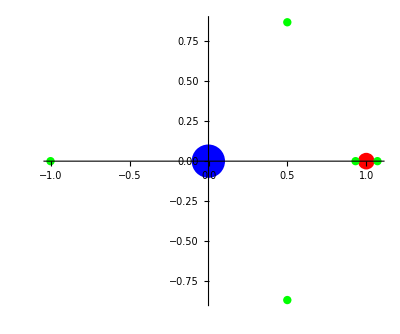

```mathematica
ClearAll["Global`*"]
μ=0.001;a=(μ/3)^(1/3);
Grid[{{Style["Σημεία Lagrange",{Underlined,Italic,15}],SpanFromLeft},{"L_1",{x1=1-μ-a+a^2/3,y1=0}},{"L_2",{x2=1-μ+a+a^2/3,y2=0}},{"L_3",{x3=-1-μ+(7μ)/(12(1-μ)),y3=0}},{"L_4",{x4=1/2-μ,y4=(√3)/2}},{"L_5",{x5=1/2-μ,y5=(-√3)/2}}}]//N
r1[t]=√((x[t]+μ)^2+y[t]^2);r2[t]=√((x[t]-1+μ)^2+y[t]^2);
deq1=x''[t]==2y'[t]+x[t]-(1-μ)(x[t]+μ)/r1[t]^3-μ(x[t]-(1-μ))/r2[t]^3;
deq2=y''[t]==-2x'[t]+y[t]-(1-μ)y[t]/r1[t]^3-μ y[t]/r2[t]^3;
bodies=Graphics[{
Blue,PointSize[0.06],Point[{-μ,0}],
Red,PointSize[0.03],Point[{1-μ,0}],
Green,PointSize[0.015],Point[{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}}]
},Axes->True,AxesOrigin->{0,0}]
```

Τροχιά κοντά στο L_1

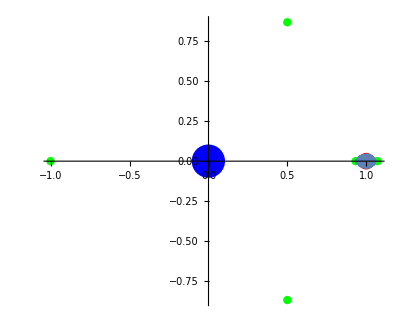

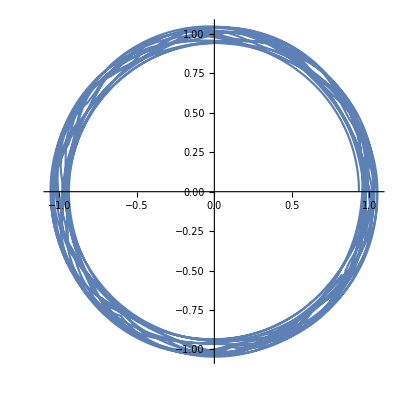

```mathematica
ClearAll[tmax,XX,YY,xx,yy,sol,p,t,IVP]
tmax=100;
IVP={deq1,deq2,x[0]==x1+0.001,y[0]==y1+0.001,x'[0]==0,y'[0]==0};
sol=NDSolve[IVP,{x[t],y[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];
yy=y[t]/.sol[[1]];
p=ParametricPlot[{xx,yy},{t,0,tmax}];
Show[{bodies,p}]
XX=xx*Cos[t]-yy*Sin[t];
YY=xx*Sin[t]+yy*Cos[t];
ParametricPlot[{XX,YY},{t,0,tmax}]
```

Τροχιά κοντά στο L_2

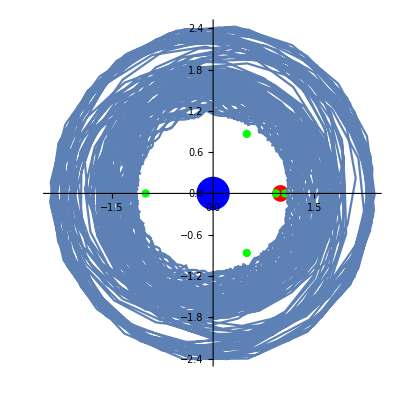

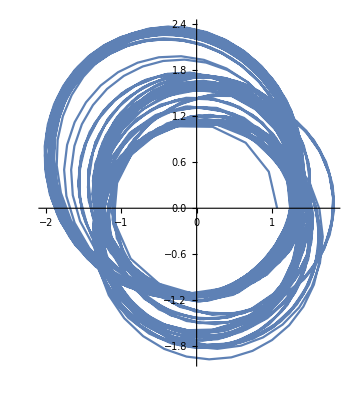

```mathematica
ClearAll[tmax,XX,YY,xx,yy,sol,p,t,IVP]
tmax=1500;
IVP={deq1,deq2,x[0]==x2+0.001,y[0]==y2+0.001,x'[0]==0,y'[0]==0};
sol=NDSolve[IVP,{x[t],y[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];
yy=y[t]/.sol[[1]];
p=ParametricPlot[{xx,yy},{t,0,tmax}];
Show[{bodies,p}]
XX=xx*Cos[t]-yy*Sin[t];
YY=xx*Sin[t]+yy*Cos[t];
ParametricPlot[{XX,YY},{t,0,tmax}]
```

Τροχιά κοντά στο L_3

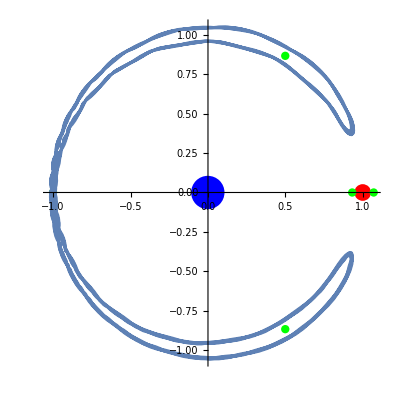

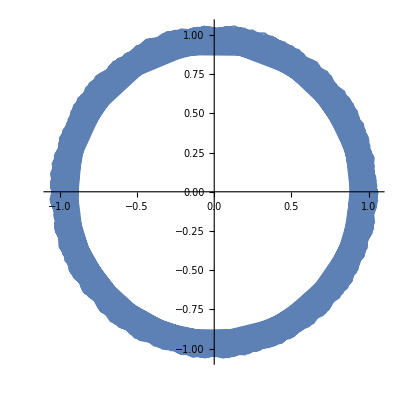

```mathematica
ClearAll[tmax,XX,YY,xx,yy,sol,p,t,IVP]
tmax=2000;
IVP={deq1,deq2,x[0]==x3+0.001,y[0]==y3+0.001,x'[0]==0,y'[0]==0};
sol=NDSolve[IVP,{x[t],y[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];
yy=y[t]/.sol[[1]];
p=ParametricPlot[{xx,yy},{t,0,tmax}];
Show[{bodies,p}]
XX=xx*Cos[t]-yy*Sin[t];
YY=xx*Sin[t]+yy*Cos[t];
ParametricPlot[{XX,YY},{t,0,tmax}]
```

Τροχιά κοντά στο L_4

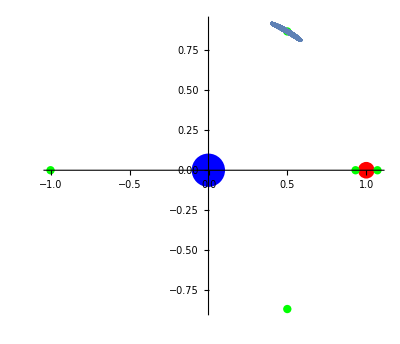

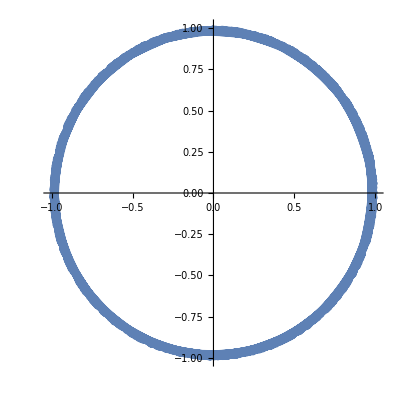

```mathematica
ClearAll[tmax,XX,YY,xx,yy,sol,p,t,IVP]
tmax=1500;
IVP={deq1,deq2,x[0]==x4+0.001,y[0]==y4+0.001,x'[0]==0,y'[0]==0};
sol=NDSolve[IVP,{x[t],y[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];
yy=y[t]/.sol[[1]];
p=ParametricPlot[{xx,yy},{t,0,tmax}];
Show[{bodies,p}]
XX=xx*Cos[t]-yy*Sin[t];
YY=xx*Sin[t]+yy*Cos[t];
ParametricPlot[{XX,YY},{t,0,tmax}]
```

Τροχιά κοντά στο L_5

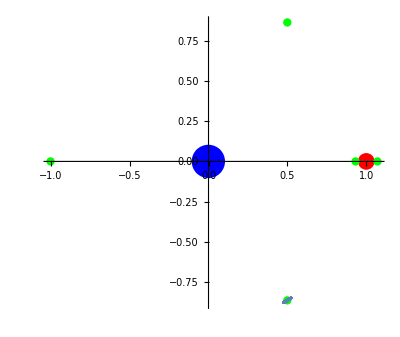

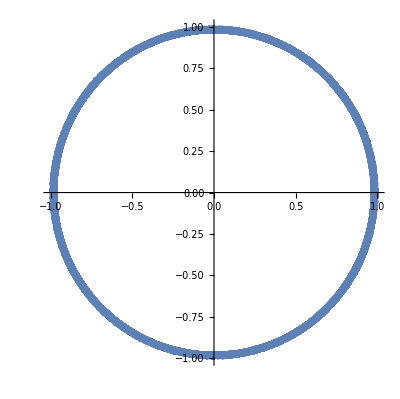

```mathematica
ClearAll[tmax,XX,YY,xx,yy,sol,p,t,IVP]
tmax=1500;
IVP={deq1,deq2,x[0]==x5+0.001,y[0]==y5+0.001,x'[0]==0,y'[0]==0};
sol=NDSolve[IVP,{x[t],y[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];
yy=y[t]/.sol[[1]];
p=ParametricPlot[{xx,yy},{t,0,tmax}];
Show[{bodies,p}]
XX=xx*Cos[t]-yy*Sin[t];
YY=xx*Sin[t]+yy*Cos[t];
ParametricPlot[{XX,YY},{t,0,tmax}]
```

Άσκηση 6.3

Στο σύστημα Ήλιος-Δίας (μ=0.001) θεωρούμε αστεροειδή που (χωρίς τη διαταραχή του Δία) κινείται σε έλλειψη με εκκεντρότητα e=0.3 και περίοδο διπλάσια αυτής του Δία. Βρείτε τις αρχικές συνθήκες του αστεροειδή για τις περιπτώσεις που ο αστεροειδής βρίσκεται για t=0 στο περίκεντρο ή στο απόκεντρο της ελλειπτικής τροχιάς.

Για αυτές τις αρχικές συνθηκες ολοκληρώστε τις εξισώσεις RTBP και σχεδιάστε την χρονική εξέλιξη του μεγάλου ημιάξονα και της εκκεντρότητας της τροχιάς του αστεροειδή.

Λύση

```mathematica
ClearAll["Global`*"]
μ=0.001;e0=0.3;T=4π;(* m0 = G M *)m0=1-μ;ω=(2π)/T;
```

Για τον αστεροειδή έχουμε T=2π √(a^3/m_0), επομένως

```mathematica
StringForm["a = ``",a=((m0 T)/(4 π^2))^(1/3)]
```

a = 0.682556

Από την εκκεντρότητα και τον μεγάλο ημιάξονα υπολογίζουμε τις αποστάσεις του περικέντρου και αποκέντρου.

```mathematica
StringForm["r_min = ``",rmin=a(1-e0)]
StringForm["r_max = ``",rmax=a(1+e0)]
```

r_min = 0.477789

r_max = 0.887323

Ορίζουμε την βοηθητική συνάρτηση που μετατρέπει τις καρτεσιανές θέσεις και ταχύτητες του αστεροειδή σε στοιχεία τροχιάς Kepler.

```mathematica
CartesianToKepler3D[r_List,u_List,t_,μ_:1]:=Module[
{
c,h,a,e,i,Ω,cosΩ,sinΩ,ω,cosωf,sinωf,M,cosE,sinE,EE,f,cosf,sinf,n,angle,T,τ
},
(* υπολογίζουμε την ενέργεια και την στροφορμή *)
c=1/2 Norm[u]^2-μ/Norm[r];h=Cross[r,u];
(* διακόπτουμε τη ροή αν η ενέργεια βγει θετική - μας ενδιαφέρουν μόνο οι κλειστές τροχιές *)
If[c>0,Return[Style["Θετική ενέργεια --- Η τροχιά δεν είναι δέσμια.",{Red,Italic}]]];
(* υπολογίζουμε τα στοιχεία της τροχιάς *)
	(* μεγάλος ημιάξονας *)a=-μ/(2c);
	(* εκκεντρότητα *)e=√(1+(2c Norm[h]^2)/μ^2);
	(* κλίση της τροχιάς *)i=ArcCos[h[[3]]/Norm[h]];
	(* μήκος του αναβιβάζοντος δεσμού *)sinΩ=Sign[h[[3]]] h[[1]]/(Norm[h]Sin[i]);cosΩ=-Sign[h[[3]]] h[[2]]/(Norm[h]Sin[i]);Ω=Mod[#,2π]&[ArcTan[cosΩ,sinΩ]];
	(* Ε *)cosE=(a-Norm[r])/(a e)sinE=(r.u)/(e √(μ a))EE=Mod[#,2π]&[ArcTan[cosE,sinE]];
	(* n *)n=μ^(1/2)a^(-3/2);
	(* μέση ανωμαλία   M=E-e sinE *)M=EE-e sinE;
	(* αληθής ανωμαλία f *)cosf=(cosE-e)/(1-e cosE)sinf=(√(1-e^2)sinE)/(1-e cosE)f=Mod[#,2π]&[ArcTan[cosf,sinf]];
	(* γωνία περικέντρου ω *)cosωf=(r[[1]] cosΩ+r[[2]]sinΩ)/Norm[r];sinωf=r[[3]]/(Norm[r] Sin[i]);ω=Mod[#,2π]&[ArcTan[cosωf,sinωf]-f];
	(* περίοδος *)T=2π √(a^3/μ);
	(* τ *)τ=t-M/n;
(* επιστρέφουμε τα αποτελέσματα *)Association["a"->a,"e"->e,"i"->i,"Ω"->Ω,"ω"->ω,"M"->M,"τ"->τ,"T"->T,"n"->n]
]
e[ttt_]:=Quiet@CartesianToKepler3D[{XX/.t->ttt,YY/.t->ttt,0},{UX/.t->ttt,UY/.t->ttt,0},ttt]["e"];
```

Α Περίπτωση

Θεωρούμε ότι το περίκεντρο και το απόκεντρο βρίσκονται πάνω στην ευθεία που ενώνει τον Ήλιο με τον Δία κατά την αρχική στιγμή.

Η αρχική θέση του δορυφόρου θα είναι σε κάθε περίπτωση η:

```mathematica
StringForm["Περίκεντρο: r_περ = (-``, 0)",rmin]
StringForm["Απόκεντρο: r_απ = (``, 0)",rmax]
```

Περίκεντρο: r_περ = (-0.477789, 0)

Απόκεντρο: r_απ = (0.887323, 0)

Η ενέργεια του δορυφόρου υπολογίζεται πάλι απ’ τον μεγάλο ημιάξονα: a=-m_0/(2 C)

```mathematica
StringForm["C = ``",c=-m0/(2a)]
```

C = -0.731808

Στο περίκεντρο και στο απόκεντρο η ταχύτητα του αστεροειδή έχει μόνο y συνιστώσα. Επομένως, την υπολογίζουμε από την ενέργεια: C=1/2 u^2-m_0/(|r|)

```mathematica
StringForm["Περίκεντρο: u_περ = (0, ``)",uper=√(2c+(2m0)/rmin)]
StringForm["Απόκεντρο: u_απ = (0, ``)",uap=√(2c+(2m0)/rmax)]
```

Περίκεντρο: u_περ = (0, 1.64868)

Απόκεντρο: u_απ = (0, 0.88775)

Οι εξισώσεις του RTBP είναι οι παρακάτω:

```mathematica
r1[t]=√((x[t]+μ)^2+y[t]^2);r2[t]=√((x[t]-1+μ)^2+y[t]^2);
deq1=x''[t]==2y'[t]+x[t]-(1-μ)(x[t]+μ)/r1[t]^3-μ(x[t]-(1-μ))/r2[t]^3;
deq2=y''[t]==-2x'[t]+y[t]-(1-μ)y[t]/r1[t]^3-μ y[t]/r2[t]^3;
```

Ορίζουμε το πρόβλημα των αρχικών συνθηκών, για την κάθε περίπτωση, και το λύνουμε. Έπειτα, διαμερίζουμε το διάστημα του χρόνου (0, t_max) και για κάθε στιγμή υπολογίζουμε την εκκεντρότητα της τροχιάς με βάση την αντίστοιχη θέση και ταχύτητα του αστεροειδή (με τη βοήθεια της συνάρτησης CartesianToKepler).

Αρχική θέση στο περίκεντρο, ο δορυφόρος κινείται σε φάση με τον Δία

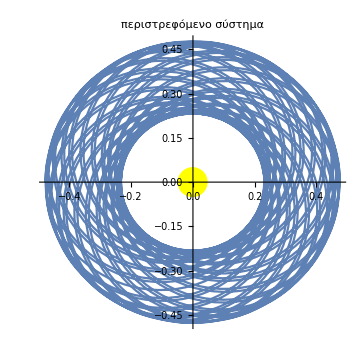
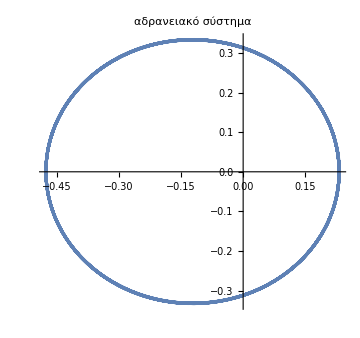
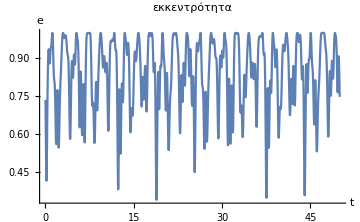
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==-rmin,y[0]==0,x'[0]==0,y'[0]==uper};
tmax=50;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής παραμένει σε τροχιά που περιορίζεται σε δακτύλιο μεταξύ Ήλιου και Δία.

Αρχική θέση στο περίκεντρο, ο δορυφόρος κινείται σε αντίθετη φάση με τον Δία

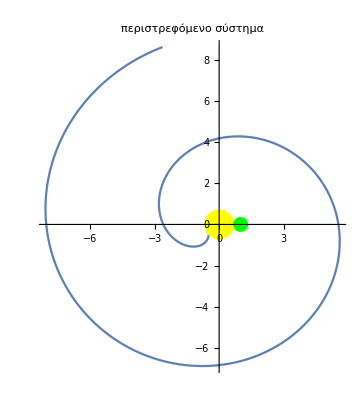
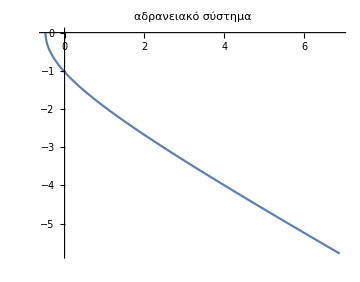
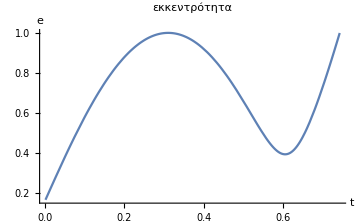
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==-rmin,y[0]==0,x'[0]==0,y'[0]==-uper};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"},PlotRange->All];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει στο άπειρο.

Αρχική θέση στο απόκεντρο, ο δορυφόρος κινείται σε φάση με τον Δία

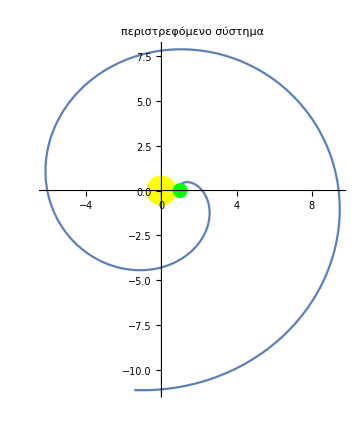
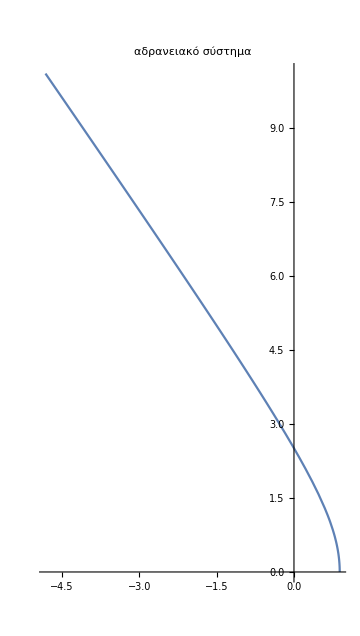
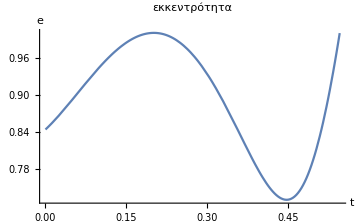
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==rmax,y[0]==0,x'[0]==0,y'[0]==uap};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"},PlotRange->All];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει στο άπειρο.

Αρχική θέση στο απόκεντρο, ο δορυφόρος κινείται σε αντίθετη φάση με τον Δία

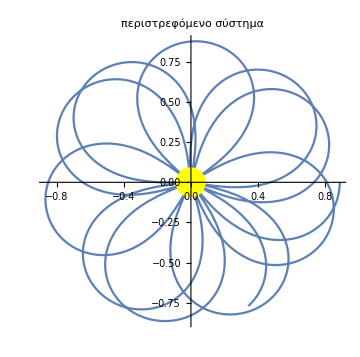
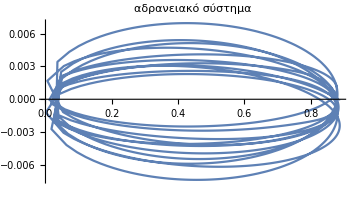
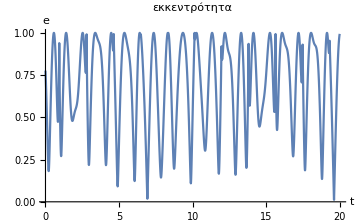
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==rmax,y[0]==0,x'[0]==0,y'[0]==-uap};
tmax=20;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"},PlotRange->All];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Φαίνεται ότι ο αστεροειδής προσκρούει στον Ήλιο.

Β Περίπτωση

Θεωρούμε ότι το περίκεντρο και το απόκεντρο βρίσκονται πάνω σε ευθεία κάθετη σ’ αυτήν που ενώνει τον Ήλιο με τον Δία κατά την αρχική στιγμή, με το περίκεντρο στα θετικά y.

Η αρχική θέση του δορυφόρου θα είναι σε κάθε περίπτωση η:

```mathematica
StringForm["Περίκεντρο: r_περ = (0, ``)",rmin]
StringForm["Απόκεντρο: r_απ = (, -``)",rmax]
```

Περίκεντρο: r_περ = (0, 0.477789)

Απόκεντρο: r_απ = (, -0.887323)

Η ενέργεια του δορυφόρου υπολογίζεται πάλι απ’ τον μεγάλο ημιάξονα: a=-m_0/(2 C)

```mathematica
StringForm["C = ``",c=-m0/(2a)]
```

C = -0.731808

Στο περίκεντρο και στο απόκεντρο η ταχύτητα του αστεροειδή έχει μόνο y συνιστώσα. Επομένως, την υπολογίζουμε από την ενέργεια: C=1/2 u^2-m_0/(|r|)

```mathematica
StringForm["Περίκεντρο: u_περ = (``, 0)",uper=√(2c+(2m0)/rmin)]
StringForm["Απόκεντρο: u_απ = (``, 0)",uap=√(2c+(2m0)/rmax)]
```

Περίκεντρο: u_περ = (1.64868, 0)

Απόκεντρο: u_απ = (0.88775, 0)

Οι εξισώσεις του RTBP είναι οι παρακάτω:

```mathematica
r1[t]=√((x[t]+μ)^2+y[t]^2);r2[t]=√((x[t]-1+μ)^2+y[t]^2);
deq1=x''[t]==2y'[t]+x[t]-(1-μ)(x[t]+μ)/r1[t]^3-μ(x[t]-(1-μ))/r2[t]^3;
deq2=y''[t]==-2x'[t]+y[t]-(1-μ)y[t]/r1[t]^3-μ y[t]/r2[t]^3;
```

Ορίζουμε το πρόβλημα των αρχικών συνθηκών, για την κάθε περίπτωση, και το λύνουμε. Έπειτα, διαμερίζουμε το διάστημα του χρόνου (0, t_max) και για κάθε στιγμή υπολογίζουμε την εκκεντρότητα της τροχιάς με βάση την αντίστοιχη θέση και ταχύτητα του αστεροειδή (με τη βοήθεια της συνάρτησης CartesianToKepler).

Αρχική θέση στο περίκεντρο, ο δορυφόρος κινείται σε φάση με τον Δία

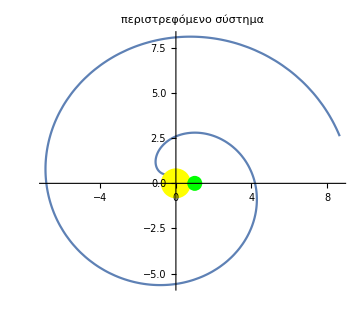
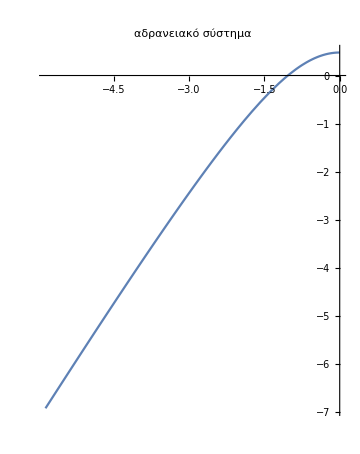
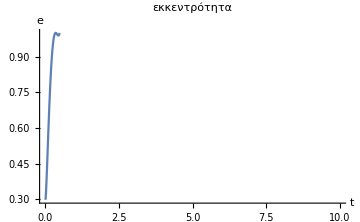
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==0,y[0]==rmin,x'[0]==-uper,y'[0]==0};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει από το σύστημα.

Αρχική θέση στο περίκεντρο, ο δορυφόρος κινείται σε αντίθετη φάση με τον Δία

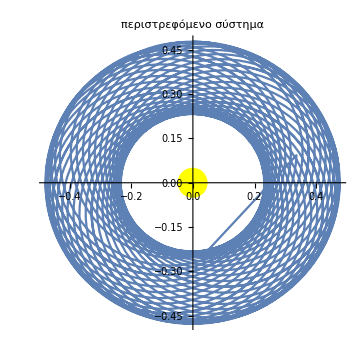
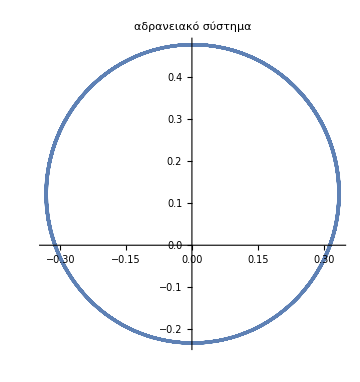
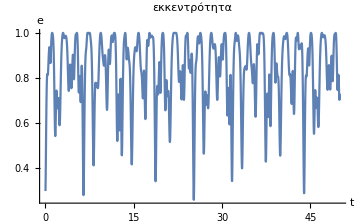
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==0,y[0]==rmin,x'[0]==uper,y'[0]==0};
tmax=50;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής κινείται μέσα σε δακτύλιο, στην περιοχή ανάμεσα σε Ήλιο-Δία.

Αρχική θέση στο απόκεντρο, ο δορυφόρος κινείται σε φάση με τον Δία

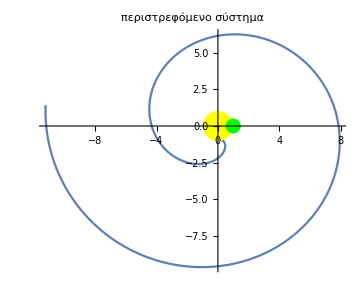
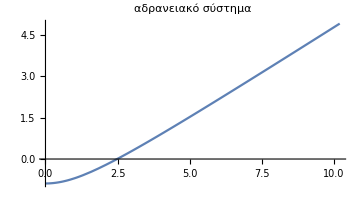
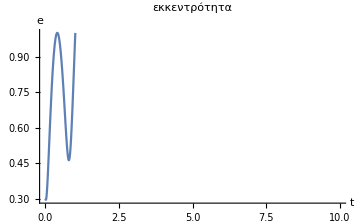
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==0,y[0]==-rmax,x'[0]==uap,y'[0]==0};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει από το σύστημα.

Αρχική θέση στο απόκεντρο, ο δορυφόρος κινείται σε αντίθετη φάση με τον Δία

NDSolve::ndsz: At t == 0.92803, step size is effectively zero; singularity or stiff system suspected.

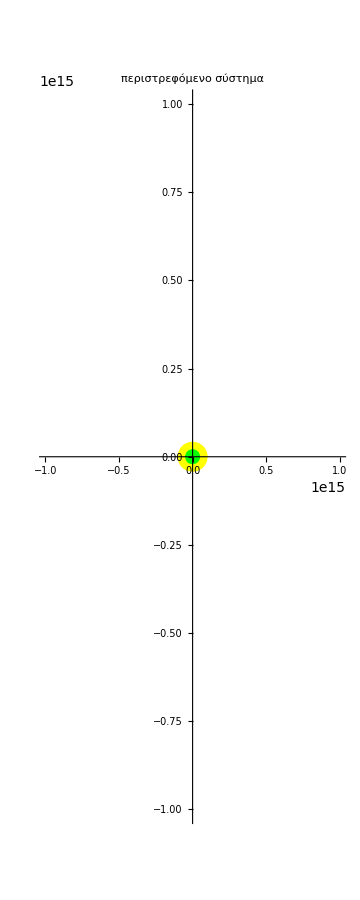
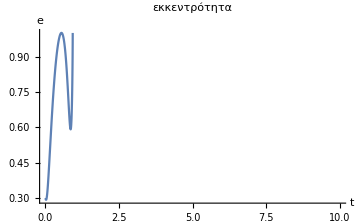
Κίνηση του Δορυφόρου
-Graphics--Graphics-
-Graphics-

```mathematica
IVP={deq1,deq2,x[0]==0,y[0]==-rmax,x'[0]==-uap,y'[0]==0};
tmax=10;
bodies={Yellow,PointSize[0.06],Point[{-μ,0}],Green,PointSize[0.03],Point[{1-μ,0}]};
sol=NDSolve[IVP,{x[t],y[t],x'[t],y'[t]},{t,0,tmax}];
xx=x[t]/.sol[[1]];yy=y[t]/.sol[[1]];
ux=x'[t]/.sol[[1]];uy=y'[t]/.sol[[1]];
ppp=ParametricPlot[{xx,yy},{t,0,tmax},PlotLabel->"περιστρεφόμενο σύστημα",Epilog->bodies,ImageSize->Medium];
XX=xx*Cos[t]-yy*Sin[t];YY=xx*Sin[t]+yy*Cos[t];
UX=(ux+xx ω)Cos[ω t]-(xx ω-uy)Sin[ω t];
UY=(uy-xx ω)Cos[ω t]-(ux+yy ω)Sin[ω t];
aaa=ParametricPlot[{XX,YY},{t,0,tmax},PlotLabel->"αδρανειακό σύστημα",ImageSize->Medium];
eee=Plot[e[ttt],{t,0,tmax},ImageSize->Medium,PlotLabel->"εκκεντρότητα",AxesLabel->{"t","e"}];
Column[{
Style["Κίνηση του Δορυφόρου",{Bold,20}],
Row[{ppp,aaa}],
eee
},Alignment->Center]
```

Ο αστεροειδής διαφεύγει από το σύστημα.

Άσκηση 6.4

Στο περιορισμένο πρόβλημα Γη-Σελήνη-Σκάφος (μ=0.0123) βρείτε τις αρχικές συνθήκες (σημείο Α) για μια τροχιά που να ξεκινάει από περιοχή “κοντά στη Γη” και η οποία πλησιάζει κοντά στη Σελήνη (σημείο Β).

Σχεδιάστε την τροχιά σοτ περιστρεφόμενο και στο αδρανειακό σύστημα από το Α στο Β (στο αδρανειακό να φαίνεται και η τροχιά της Σελήνης).

Σε ποια ενέργεια C_J αντιστοιχεί; (απαίτηση της άσκησης C_J<1.1)

Κάντε μετατροπή και δώστε σε φυσικές μονάδες τις αρχικές συνθήκες στο Α και τις τελικές στο Β.

Λύση

Άσκηση 6.5

Ένας εξωπλανήτης κινείται γύρω από ένα διπλό σύστημα αστέρωμ με μάζες m_1 και m_2. Εντοπίστε με την τομή Poincare τις περιοχές με ευσταθή (κανονική) κίνηση για τις παρακάτω παραμέτρους:

m_1=0.9, m_2=0.1, C_J=-2, C_J=-1.9, C_J=-1.8, C_J=-1.6

m_1=0.8, m_2=0.2, C_J=-2, C_J=-1.9, C_J=-1.8, C_J=-1.6

m_1=0.6, m_2=0.4, C_J=-2, C_J=-1.9, C_J=-1.8, C_J=-1.6

m_1=0.5, m_2=0.5, C_J=-2, C_J=-1.9, C_J=-1.8, C_J=-1.6

Σχεδιάστε κάποιες περιοδικές τροχιές που έχετε εντοπίσει στο περιστρεφόμενο και στο αδρανειακό σύστημα.

Σχολιάστε σύντομα τα αποτελέσματά σας.

Λύση